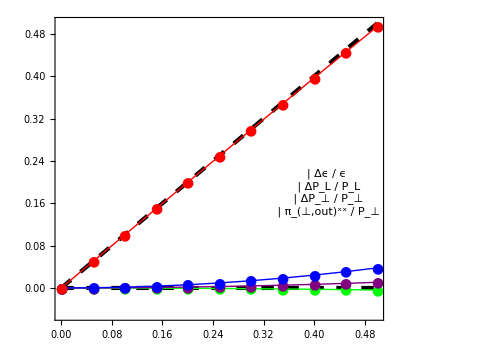

```mathematica
(*ANISOTROPIC HADRON RESONANCE GAS*)

T0 = 0.155;
αT = 1.0;
αL = 1.0;
Λ = 0.155; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,0.0001067,0.000427,0.0009608,0.001708,0.00267,0.003845,0.005234,0.006837,0.008655,0.01069};

ΔPLoverPLdata = {0.0,-3.814*10^-05,-0.0001527,-0.0003438,-0.0006122,-0.0009583,-0.001383,-0.001888,-0.002473,-0.003141,-0.003894};

ΔPToverPTdata ={0.0,0.0003785,0.001514,0.003408,0.00606,0.009471,0.01364,0.01858,0.02428,0.03075,0.03799};

piperpoverPTdata = {0.0,0.04999,0.09995,0.1498,0.1996,0.2492,0.2987,0.3479,0.3968,0.4455,0.4938};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δϵ / ϵ",FontSize->16]},

{Graphics[{Green,Disk[]},ImageSize->10],Style["ΔP_L / P_L",FontSize->16]},{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP_⊥ / P_⊥",FontSize->16]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["π_(⊥,out)^xx / P_⊥",FontSize->16]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.-0.05,0.5},ImageSize->{500,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔPLoverPLplot,Δϵoverϵplot,ΔPToverPTplot,piperpoverPTplot},Joined->{True},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,14},{●,14},{●,14},{●,14}},PlotStyle->{{Green,Thick},{Purple,Thick},{Blue,Thick},{Red,Thick}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.42,0.18}]},ImageSize->{500,400},FrameLabel->{"π_(⊥,in)^xx / P_⊥"}]
```